# Cálculo Numérico(MAT012) Atividade 1

## UNIVERSIDADE FEDERAL DE ITAJUBÁ UNIFEI

Luis Roberto Costa Dias - 21783
Fernando Belo Anacleto Granco - 22007

Dados iniciais

Não se esqueça: para executar cada célula pressione SHIFT+ENTER juntos.

```mathematica
Clear[f,df,maxit,eps];

(* Funcao e primeira derivada *)

f[x_]:=10x*E^(-2x)+E^(-x)-2;
df[x_]:=-(E^(-2 x))*(-10+E^x+20 x);

(* Numero maximo de iteracoes e tolerancia *)

maxit = 500;
eps=0.000001;
```

INICIO DO EXERCICIO

```mathematica
Solve[10x*E^(-2x)+E^(-x)-2==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-2+ⅇ^-x+10 ⅇ^(-2 x) x==0,x]

Podemos ver que não é possível resolver a equação descrita através do método padrão da função Solve[]. Para isso, nas partes seguintes, iremos implementar os métodos vistos em sala de aula a fim de identificar as raízes da equação.

```mathematica
Questãoa)
```

Faça no espaço abaixo o gráfico da função f(x) que define a equação f(x) = 0.

```mathematica
Plot[{f[x],df[x]},{x,-0.5,2},PlotTheme->"Scientific"]
```

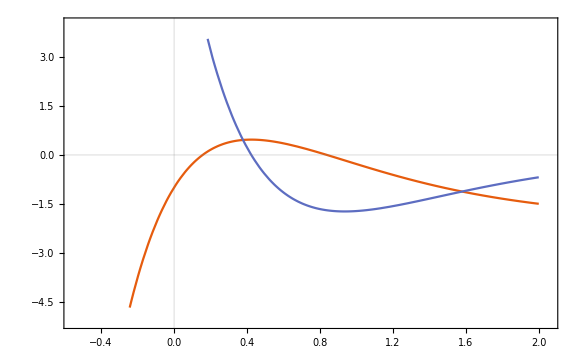

Com a ajuda do gráfico acima, é possível identificar os possíveis lugares das raízes de f(x), representada pela linha laranja.

```mathematica
Questão b)
```

A seguir, serão implementados os métodos vistos em sala para identificar as raízes da função de acordo com as especificações solicitadas.

Método da Bisseção

```mathematica
Clear[a, b, k, x];

(* Intervalo inicial *)

a=0;
b=0.5;

(* Loop principal *)

k=1;

While[
k≤ maxit,
x=(a+b)/2;
If[f[a]*f[x]<0,b=x,a=x];
If[
Abs[b-a]<eps||Abs[f[x]]<eps,
Print["x = ",x,"   f(x) = ",f[x],"   it = ",k];
Break[]
];
k++
];
```

x = 0.156611   f(x) = 2.0375×10^-6   it = 19

```mathematica
Clear[a, b, k, x];

(* Intervalo inicial *)

a=0.5;
b=1;

(* Loop principal *)

k=1;

While[
k≤ maxit,
x=(a+b)/2;
If[f[a]*f[x]<0,b=x,a=x];
If[
Abs[b-a]<eps||Abs[f[x]]<eps,
Print["x = ",x,"   f(x) = ",f[x],"   it = ",k];
Break[]
];
k++
];
```

x = 0.838382   f(x) = 3.83067×10^-7   it = 19

Método de Newton

```mathematica
Clear[x0,x1,k];

(* Chute inicial *)

x0=0.1;

(* Loop principal *)

k=1;

While[
k≤ maxit,
x1=x0-(f[x0]/df[x0]);
(* Imprime por iteracao
Print[ ];
Print["x = ",x1,"   f(x) = ",f[x1],"   it = ",k];
Print[ ];*)
If[
Abs[x1-x0]<eps|| Abs[f[x1]]<eps,
Print["x = ",x1, "  f(x) = ", f[x1], "   it = ", k];
Break[]
];
x0=x1;
k++
];
```

x = 0.156611  f(x) = -3.14092×10^-7   it = 3

```mathematica
Clear[x0,x1,k];

(* Chute inicial *)

x0=0.6;

(* Loop principal *)

k=1;

While[
k≤ maxit,
x1=x0-(f[x0]/df[x0]);
(* Imprime por iteracao
Print[ ];
Print["x = ",x1,"   f(x) = ",f[x1],"   it = ",k];
Print[ ];*)
If[
Abs[x1-x0]<eps|| Abs[f[x1]]<eps,
Print["x = ",x1, "  f(x) = ", f[x1], "   it = ", k];
Break[]
];
x0=x1;
k++
];
```

x = 0.838382  f(x) = -1.11258×10^-7   it = 3

Método da Secante

```mathematica
Clear[x0,x1,x2,k];

(* Chutes iniciais *)

x0=0.2;
x1=0.5;

(* Loop principal *)

k=1;

While[
k≤ maxit,
x2=(x0*f[x1]-x1*f[x0])/(f[x1]-f[x0]);
If[
Abs[x2-x1]<eps|| Abs[f[x2]]<eps,
Print["x = ",x2, "  f(x) = ", f[x2], "   it = ", k];
Break[]
];
x0=x1;
x1=x2;
k++
];
```

x = 0.156611  f(x) = 2.96875×10^-7   it = 8

```mathematica
Clear[x0,x1,x2,k];

(* Chutes iniciais *)

x0=0.6;
x1=1;

(* Loop principal *)

k=1;

While[
k≤ maxit,
x2=(x0*f[x1]-x1*f[x0])/(f[x1]-f[x0]);
If[
Abs[x2-x1]<eps|| Abs[f[x2]]<eps,
Print["x = ",x2, "  f(x) = ", f[x2], "   it = ", k];
Break[]
];
x0=x1;
x1=x2;
k++
];
```

x = 0.838382  f(x) = 8.05351×10^-11   it = 4

```mathematica
Conclusão
```

Foi possível constatar a eficiência do método de Newton para encontrar raízes reais para a equação sugerida.Fatores como a escolha dos pontos de referência foram essenciais para o resultado obtido, o que só foi possível graças ao processamento do gráfico por parte do programa.

```mathematica
Questão c)
FindMaximum[f[x],{x,0}]
```

{2.47029,{-0.0912771→0.423626}}

```mathematica
Questão Extra
```

```mathematica
g[x_]:=E^(x)-E^(-x)-3*x;
dg[x_]:=-3+E^(-x)+E^x;
```

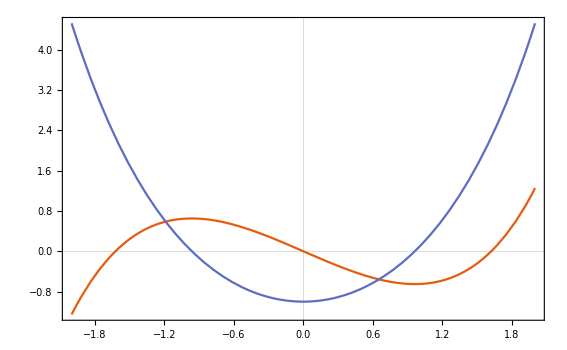

```mathematica
Plot[{g[x],dg[x]},{x,-2,2},PlotTheme->"Scientific"]
```

### Primeiro Intervalo Possível de raízes [-2,-1]

```mathematica
Clear[l,u,k];

l=-2.0;
u=-1.0;
x0=1.45;
x1=0.0;
k=1;
maxit=500;
eps=0.000001;
If[(g[l]*g[u])<0,
x0=u;
k=0;
Print["Condição Inicial Atendida"];
While[k<=maxit,
If[Abs[g[x0]]<eps||u-l<eps,
Print["x0=",x0,"\n Número total de iterações:",k+1];
Break[]];
x1=x0-(g[x0]/dg[x0]);
If[l<x1<u&&(Abs[g[x1]]≤0.99*Abs[g[x0]]),
x0=x1,
x0=(l+u)/2;
If[g[l]*g[x0]<0,
u=x0,
l=x0;
];
];
k++;
];,
Print["Condição Inicial Não Atendida"]
];
```

Condição Inicial Atendida

x0=-1.62213
 Número total de iterações:5

### Segundo Intervalo Possível de raízes [-1,1]

```mathematica
Clear[l,u,k];

l=-1.0;
u=1.0;
x0=1.45;
x1=0.0;
k=1;
maxit=500;
eps=0.000001;
If[(g[l]*g[u])<0,
x0=u;
k=0;
Print["Condição Inicial Atendida, g(u)*g(l)<0."];
While[k<=maxit,
If[Abs[g[x0]]<eps||u-l<eps,
Print["x0=",x0,"\n Número total de iterações:",k+1];
Break[]];
x1=x0-(g[x0]/dg[x0]);
If[l<x1<u&&(Abs[g[x1]]≤0.99*Abs[g[x0]]),
x0=x1,
x0=(l+u)/2;
If[g[l]*g[x0]<0,
u=x0,
l=x0;
];
];
k++;
];,
Print["Condição Inicial Não Atendida, g(u)*g(l)=>0."]
];
```

Condição Inicial Atendida, g(u)*g(l)<0.

x0=0.
 Número total de iterações:2

### Terceiro Intervalo Possível de raízes [1,2]

```mathematica
Clear[l,u,k];

l=1.0;
u=2.0;
x0=1.45;
x1=0.0;
k=1;
maxit=500;
eps=0.000001;
If[(g[l]*g[u])<0,
x0=u;
k=0;
Print["Condição Inicial Atendida, g(u)*g(l)<0."];
While[k<=maxit,
If[Abs[g[x0]]<eps||u-l<eps,
Print["x0=",x0,"\n Número total de iterações:",k+1];
Break[]];
x1=x0-(g[x0]/dg[x0]);
If[l<x1<u&&(Abs[g[x1]]≤0.99*Abs[g[x0]]),
x0=x1,
x0=(l+u)/2;
If[g[l]*g[x0]<0,
u=x0,
l=x0;
];
];
k++;
];,
Print["Condição Inicial Não Atendida, g(u)*g(l)=>0."]
];
```

Condição Inicial Atendida, g(u)*g(l)<0.

x0=1.62213
 Número total de iterações:5